## CalCoMatica settings

```mathematica
ClearAll["Global`*"]; (* clear kernel *)
dir=NotebookDirectory[]; (* this notebook directory *)
dirData="data"; (* data directory *)
dirCore="core"; (* core directory *)
SetDirectory[FileNameJoin[{dir,dirCore}]]; (* set core directory *)
<<calcomatica.m; (* load CalCoMatica package *)
<<lukpack.m ; (* load LukPack package *)
SetDirectory[dir]; (* set working directory *)
LoadParams["3CCs.stretch"]; (* load default notebook file with model parameters *)
```

## AZ model settings

```mathematica
version="2p.Wang2008_P16-P19.kfactor.V"; (* file for CalC*)
CalC["$PATH"]=False; (* use CalC from CalCoMatica directory instead of system *)
CalC["version"]="cwin691x64"; (* CalC version to be used for run: "cwin691x64" (Windows) or "cmac691" (macOS) *)

Adaptive["accuracy"]="1e-2"; (* CalC default is "1e-5" *)
gridX=gridY= 40; (* grid size in x and y direction*)
gridZ= 30; (* grid size in z direction*)

kfactor=1.065; (* kon*kfactor ; koff/kfactor *)
kreloadClose=0.0005; (* 1/ms, close pool recycling speed *)
kreloadRemote=0.03; (* 1/ms, remote pool recycling speed *)
NcStart=1;  (* initial number of vesicles in close pool*)
NrStart=4; (* initial number of vesicles in remote pool*)

CloseVesicle=0.0065; (* um, localization of close vesicles pool from MDC *)
RemoteVesicle=0.015; (* um, localization of remote vesicles pool from MDC *)

MDC={(s+s/2.),(s/2.),0}; (* "Most Distal Channel" (MDC) location *)
vesC=MDC+{CloseVesicle,0,0}; (* position of closer vesicle (sensor) *)
vesR=MDC+{RemoteVesicle,0,0}; (* position of remote vesicle (sensor) *)

Print["MDC position ",MDC," um"];
Print["closer vesicle (sensor) position ",vesC," um"];
Print["remote vesicle (sensor) position ",vesR," um"];

AddBuffer["ATP",0.22,0.5,100,370,"all Noflux"]; (* name, D, kon, koff, total, BC [Meinrenken et al. 2002] *)
AddBuffer["MobileBufferEGTA",0.22,0.005043,0.0010085,100,"all Noflux"]; (* name, D, kon, koff, total, BC [Smith et al. 1984] *)

inName={"Rc","Rr","Fc","Fr","Vc","Vr","R","F","V"}; (* data from CalC to load *) 

EGTAconcOfEGTAAM = 20000;
```

MDC position {1.5 s,0.5 s,0} um

closer vesicle (sensor) position {0.0065+1.5 s,0.5 s,0} um

remote vesicle (sensor) position {0.015+1.5 s,0.5 s,0} um

## AP run

```mathematica
runMode=1; (* single AP *)

startAP=0; (* ms, time of simulation before first AP (baseline) *)
endAP=2; (* ms, end of calculations for AP *)

PrintRunMode[]; (* display run mode name *)
```

Single AP

### No EGTA

```mathematica
RunCalC[version];

For[in=1,in≤Length[inName],in++,
ImportCalC[inName[[in]],"AP"];
];
```

### EGTA

```mathematica
AddBuffer["EGTAAM",0.22,0.005043,0.0010085,EGTAconcOfEGTAAM,"all Noflux"]; (* name, D, kon, koff, total, BC [Smith et al. 1984] *)
RunCalC[version];

For[in=1,in≤Length[inName],in++,
ImportCalC[inName[[in]],"AP_EGTAAM"];
];
RemoveBuffer["EGTAAM"];
```

## AP plots

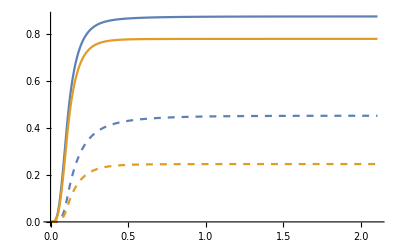

```mathematica
normAPFr={#1,#2/4}&@@@Data["AP"]["Fr"];
normAPFrEGTA={#1,#2/4}&@@@Data["AP_EGTAAM"]["Fr"];
ListLinePlot[{Data["AP"]["Fc"],normAPFr,Data["AP_EGTAAM"]["Fc"],normAPFrEGTA},PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]},PlotRange->All]
```

```mathematica
Print["Fr_max=",Max[normAPFr[[All,2]]],"\n","Fc_max=",Max[Data["AP"]["Fc"][[All,2]]]];
Print["Fr_max_EGTAAM=",Max[normAPFrEGTA[[All,2]]],"\n","Fc_max_EGTAAM=",Max[Data["AP_EGTAAM"]["Fc"][[All,2]]]];
```

Fr_max=0.451641
Fc_max=0.874129

Fr_max_EGTAAM=0.246076
Fc_max_EGTAAM=0.778767

## 300Hz run

```mathematica
runMode=2; (* train *)

startTrain=0; (* ms, time of simulation before first AP in a train (baseline) *)

PrintRunMode[]; (* display run mode name *)
```

Train [20APs @ 300Hz]

### No EGTA

```mathematica
RunCalC[version];

For[in=1,in≤Length[inName],in++,
ImportCalC[inName[[in]],"train"];
];
```

### EGTA

```mathematica
AddBuffer["EGTAAM",0.22,0.005043,0.0010085,EGTAconcOfEGTAAM,"all Noflux"]; (* name, D, kon, koff, total, BC [Smith et al. 1984] *)
RunCalC[version];

For[in=1,in≤Length[inName],in++,
ImportCalC[inName[[in]],"train_EGTAAM"];
];
RemoveBuffer["EGTAAM"];
```

## 300Hz plots

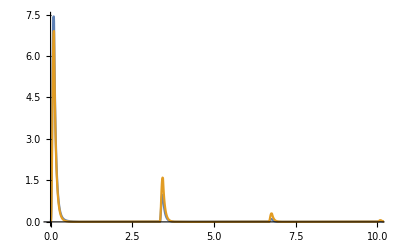

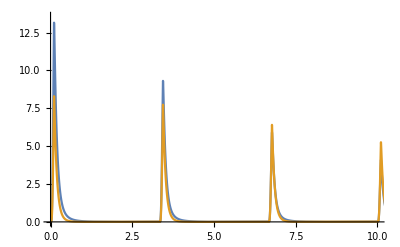

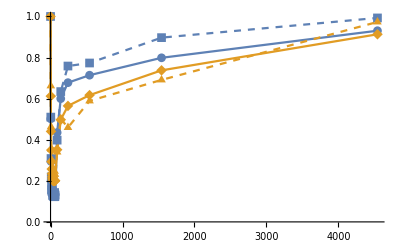
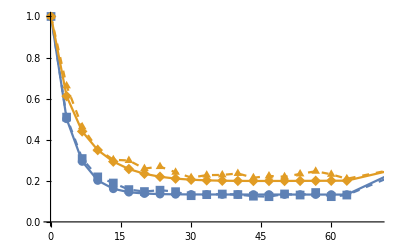
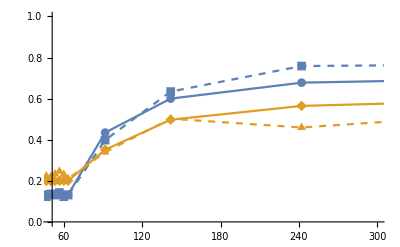
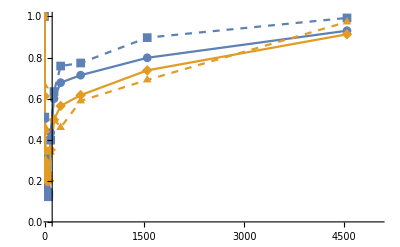

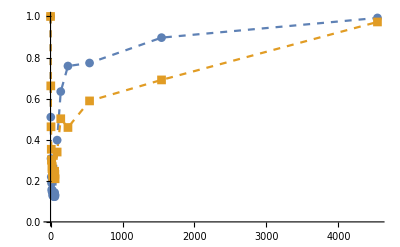
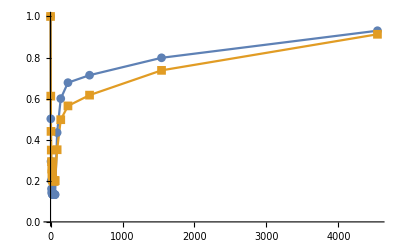

```mathematica
AllAPsTime=TimeAPs[]+time;
timeInt=0.4;

(* defined interval after stimulus (time=0.105ms) in release rate R *)
AllAPsPeak=GetY[Data["train"]["R"],AllAPsTime];
AllAPsPeakc=GetY[Data["train"]["Rc"],AllAPsTime];
AllAPsPeakr=GetY[Data["train"]["Rr"],AllAPsTime];
AllAPs=Transpose[{AllAPsTime,AllAPsPeak}];
NormAllAPs=Transpose[{AllAPs[[All,1]],AllAPs[[All,2]]/AllAPs[[1,2]]}];

(* integral of the release rate (=difference in F) from 0 tp 0.2ms after stimulus *)
AllAPsPeakInt=GetY[Data["train"]["F"],TimeAPs[]+timeInt]-GetY[Data["train"]["F"],TimeAPs[]];
AllAPsPeakIntc=GetY[Data["train"]["Fc"],TimeAPs[]+timeInt]-GetY[Data["train"]["Fc"],TimeAPs[]];
AllAPsPeakIntr=GetY[Data["train"]["Fr"],TimeAPs[]+timeInt]-GetY[Data["train"]["Fr"],TimeAPs[]];
AllAPsInt=Transpose[{AllAPsTime,AllAPsPeakInt}];
NormAllAPsInt=Transpose[{AllAPsInt[[All,1]],AllAPsInt[[All,2]]/AllAPsInt[[1,2]]}];

(* release prob. *)
vv=GetY[Data["train"]["V"],TimeAPs[]];
vvc=GetY[Data["train"]["Vc"],TimeAPs[]];
vvr=GetY[Data["train"]["Vr"],TimeAPs[]];
AllprInt=Transpose[{AllAPsTime,Clip[AllAPsPeakInt/vv,{0,1}]}];(* Clip prevents pr>1 due to rounding problems *)
AllprIntc=Transpose[{AllAPsTime,Clip[AllAPsPeakIntc/vvc,{0,1}]}];
AllprIntr=Transpose[{AllAPsTime,Clip[AllAPsPeakIntr/vvr,{0,1}]}];

(* defined interval after stimulus (time=0.105ms) in release rate R *)
AllAPsPeakEGTAAM=GetY[Data["train_EGTAAM"]["R"],AllAPsTime];
AllAPsPeakEGTAAMc=GetY[Data["train_EGTAAM"]["Rc"],AllAPsTime];
AllAPsPeakEGTAAMr=GetY[Data["train_EGTAAM"]["Rr"],AllAPsTime];
AllAPsEGTAAM=Transpose[{AllAPsTime,AllAPsPeakEGTAAM}];
NormAllAPsEGTAAM=Transpose[{AllAPsEGTAAM[[All,1]],AllAPsEGTAAM[[All,2]]/AllAPsEGTAAM[[1,2]]}];

(* integral of the release rate (=difference in F) from 0 tp 0.2ms after stimulus *)
AllAPsPeakEGTAAMInt=GetY[Data["train_EGTAAM"]["F"],TimeAPs[]+timeInt]-GetY[Data["train_EGTAAM"]["F"],TimeAPs[]];
AllAPsPeakEGTAAMIntc=GetY[Data["train_EGTAAM"]["Fc"],TimeAPs[]+timeInt]-GetY[Data["train_EGTAAM"]["Fc"],TimeAPs[]];
AllAPsPeakEGTAAMIntr=GetY[Data["train_EGTAAM"]["Fr"],TimeAPs[]+timeInt]-GetY[Data["train_EGTAAM"]["Fr"],TimeAPs[]];
AllAPsEGTAAMInt=Transpose[{AllAPsTime,AllAPsPeakEGTAAMInt}];
NormAllAPsEGTAAMInt=Transpose[{AllAPsEGTAAMInt[[All,1]],AllAPsEGTAAMInt[[All,2]]/AllAPsEGTAAMInt[[1,2]]}];

(* release prob. *)
vvEGTAAM=GetY[Data["train_EGTAAM"]["V"],TimeAPs[]];
vvEGTAAMc=GetY[Data["train_EGTAAM"]["Vc"],TimeAPs[]];
vvEGTAAMr=GetY[Data["train_EGTAAM"]["Vr"],TimeAPs[]];
AllprIntEGTAAM=Transpose[{AllAPsTime,Clip[AllAPsPeakEGTAAMInt/vvEGTAAM,{0,1}]}];
AllprIntEGTAAMc=Transpose[{AllAPsTime,Clip[AllAPsPeakEGTAAMIntc/vvEGTAAMc,{0,1}]}];
AllprIntEGTAAMr=Transpose[{AllAPsTime,Clip[AllAPsPeakEGTAAMIntr/vvEGTAAMr,{0,1}]}];

(* experiemtal data *)
experi300HzControl={124.737,63.6265,38.4777,27.3403,23.6115,19.6204,18.4274,19.2551,18.3516,15.9035,16.5407,16.9287,16.6076,15.5935,15.3023,16.9757,16.3063,17.8398,15.3126,16.2945,49.6528,79.1184,94.6361,96.477,111.88,123.845};
experi300HzControlNorm=experi300HzControl/experi300HzControl[[1]];
ExpData=Transpose[{AllAPsTime,experi300HzControlNorm}];

experi300HzEGTA={80.5039,53.3031,37.2697,28.4587,24.3574,24.0502,20.8928,21.6705,19.4482,17.356,18.3255,18.4088,18.9762,17.3061,18.0006,17.6968,18.7902,19.8404,18.6428,16.8962,27.3772,40.4195,36.9938,47.409,55.6358,78.3473};
experi300HzEGTANorm=experi300HzEGTA/experi300HzEGTA[[1]];
ExpDataEGTA=Transpose[{AllAPsTime,experi300HzEGTANorm}];

ListPlot[{Data["train"]["Rc"],Data["train_EGTAAM"]["Rc"]},PlotRange->{{0,10},All},Joined->True]
ListPlot[{Data["train"]["Rr"],Data["train_EGTAAM"]["Rr"]},PlotRange->{{0,10},All},Joined->True]

{
ListPlot[{NormAllAPs,ExpData,NormAllAPsEGTAAM,ExpDataEGTA},PlotRange->All,Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
,
ListPlot[{NormAllAPs,ExpData,NormAllAPsEGTAAM,ExpDataEGTA},PlotRange->{{0,70},All},Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
,
ListPlot[{NormAllAPs,ExpData,NormAllAPsEGTAAM,ExpDataEGTA},PlotRange->{{50,300},All},Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
,
ListPlot[{NormAllAPs,ExpData,NormAllAPsEGTAAM,ExpDataEGTA},PlotRange->{{90,5000},All},Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
}

{
ListPlot[{ExpData,ExpDataEGTA},PlotRange->All,Joined->True,PlotMarkers->Automatic,PlotStyle->{Directive[ColorData[97,1],Dashed],Directive[ColorData[97,2],Dashed]}]
,
ListPlot[{NormAllAPs,NormAllAPsEGTAAM},PlotRange->All,Joined->True,PlotMarkers->Automatic]
}
```

### Pr

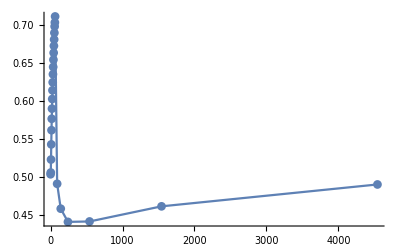
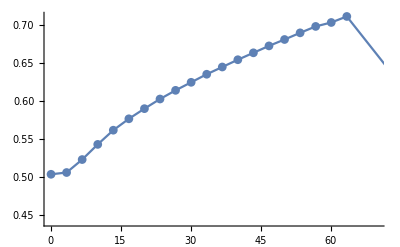
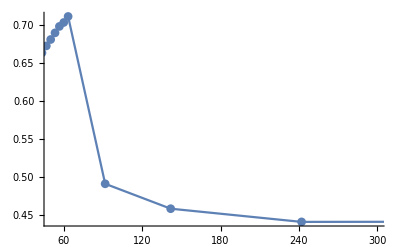
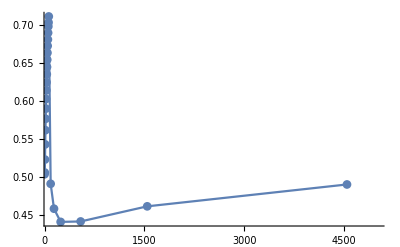

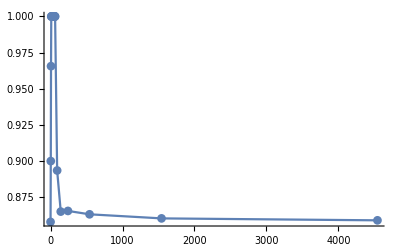
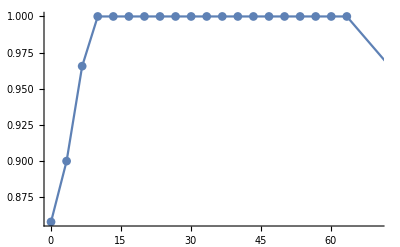
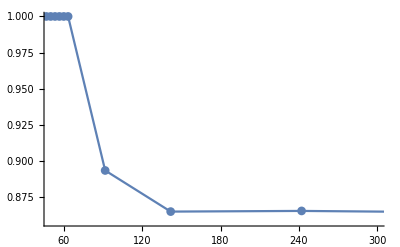
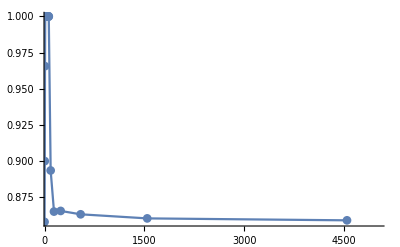

```mathematica
{
ListPlot[{AllprInt},PlotRange->All,Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
,
ListPlot[{AllprInt},PlotRange->{{0,70},All},Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
,
ListPlot[{AllprInt},PlotRange->{{50,300},All},Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
,
ListPlot[{AllprInt},PlotRange->{{90,5000},All},Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
}
{
ListPlot[{AllprIntc},PlotRange->All,Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
,
ListPlot[{AllprIntc},PlotRange->{{0,70},All},Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
,
ListPlot[{AllprIntc},PlotRange->{{50,300},All},Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
,
ListPlot[{AllprIntc},PlotRange->{{90,5000},All},Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
}
{
ListPlot[{AllprIntr},PlotRange->All,Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
,
ListPlot[{AllprIntr},PlotRange->{{0,70},All},Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
,
ListPlot[{AllprIntr},PlotRange->{{50,300},All},Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
,
ListPlot[{AllprIntr},PlotRange->{{90,5000},All},Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
}
```

### Pr EGTA

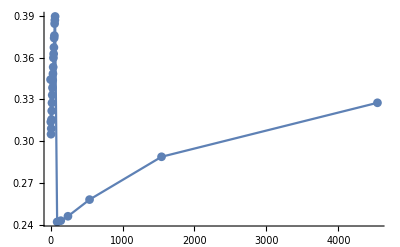
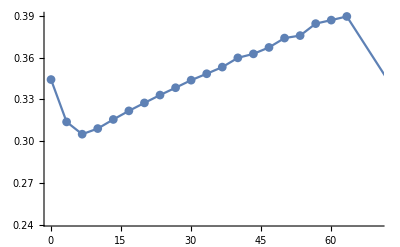
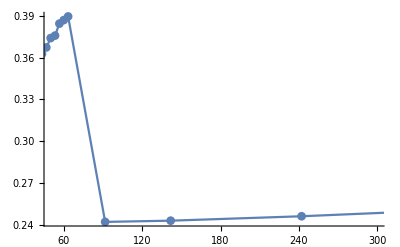
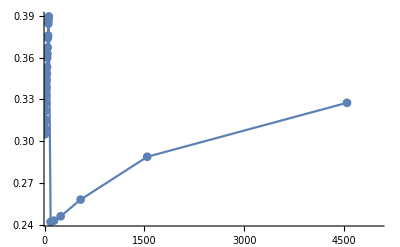

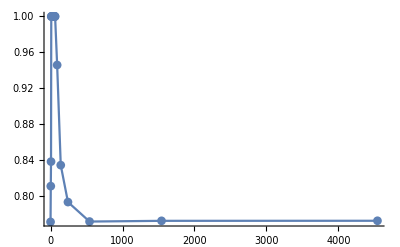
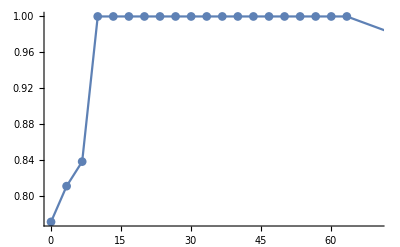
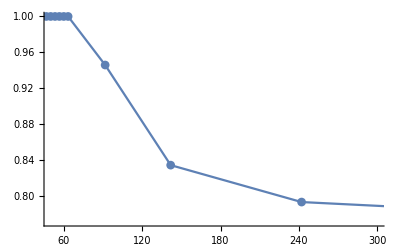
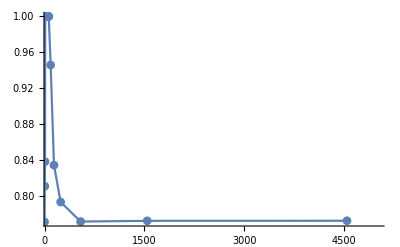

```mathematica
{
ListPlot[{AllprIntEGTAAM},PlotRange->All,Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
,
ListPlot[{AllprIntEGTAAM},PlotRange->{{0,70},All},Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
,
ListPlot[{AllprIntEGTAAM},PlotRange->{{50,300},All},Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
,
ListPlot[{AllprIntEGTAAM},PlotRange->{{90,5000},All},Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
}
{
ListPlot[{AllprIntEGTAAMc},PlotRange->All,Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
,
ListPlot[{AllprIntEGTAAMc},PlotRange->{{0,70},All},Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
,
ListPlot[{AllprIntEGTAAMc},PlotRange->{{50,300},All},Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
,
ListPlot[{AllprIntEGTAAMc},PlotRange->{{90,5000},All},Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
}
{
ListPlot[{AllprIntEGTAAMr},PlotRange->All,Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
,
ListPlot[{AllprIntEGTAAMr},PlotRange->{{0,70},All},Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
,
ListPlot[{AllprIntEGTAAMr},PlotRange->{{50,300},All},Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
,
ListPlot[{AllprIntEGTAAMr},PlotRange->{{90,5000},All},Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
}
```

### Compare release rate at 0.105 and integral

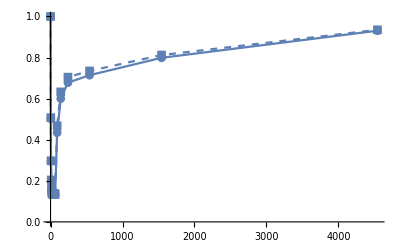
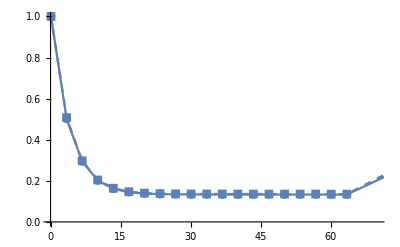
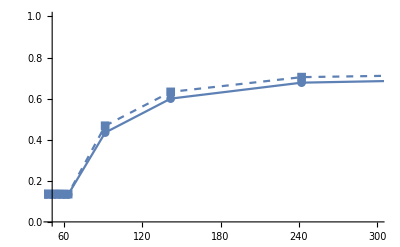
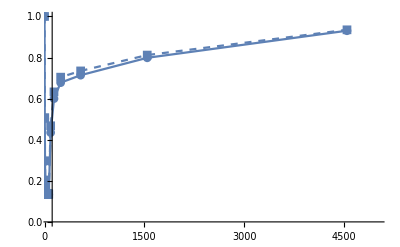

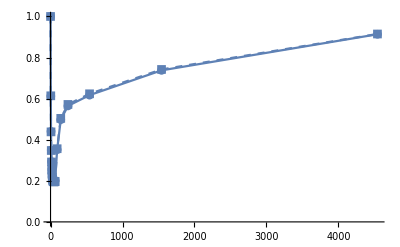
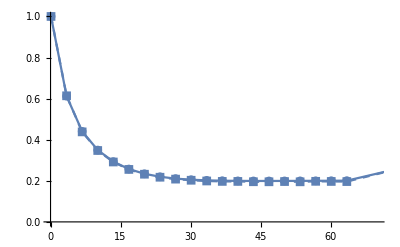
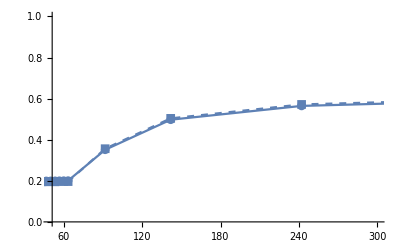
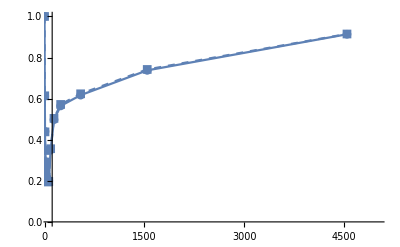

```mathematica
{
ListPlot[{NormAllAPs,NormAllAPsInt},PlotRange->All,Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
,
ListPlot[{NormAllAPs,NormAllAPsInt},PlotRange->{{0,70},All},Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
,
ListPlot[{NormAllAPs,NormAllAPsInt},PlotRange->{{50,300},All},Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
,
ListPlot[{NormAllAPs,NormAllAPsInt},PlotRange->{{90,5000},All},Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
}
{
ListPlot[{NormAllAPsEGTAAM,NormAllAPsEGTAAMInt},PlotRange->All,Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
,
ListPlot[{NormAllAPsEGTAAM,NormAllAPsEGTAAMInt},PlotRange->{{0,70},All},Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
,
ListPlot[{NormAllAPsEGTAAM,NormAllAPsEGTAAMInt},PlotRange->{{50,300},All},Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
,
ListPlot[{NormAllAPsEGTAAM,NormAllAPsEGTAAMInt},PlotRange->{{90,5000},All},Joined->True,PlotMarkers->Automatic,PlotStyle->{ColorData[97,1],Directive[ColorData[97,1],Dashed],ColorData[97,2],Directive[ColorData[97,2],Dashed]}]
}
```

### write some values - Norm releate rate at 0.105 and expermental norm. peak EPSC amplitude

```mathematica
NormAllAPs[[All,2]]
ExpData[[All,2]]
```

{1.,0.501813,0.294248,0.201575,0.161236,0.14455,0.137899,0.135268,0.134204,0.133722,0.133489,0.133357,0.133273,0.133223,0.133176,0.133134,0.133092,0.133036,0.132978,0.132902,0.43464,0.600078,0.677746,0.714118,0.798749,0.930557}

{1.,0.510085,0.308471,0.219184,0.18929,0.157294,0.14773,0.154366,0.147122,0.127496,0.132605,0.135715,0.133141,0.125011,0.122677,0.136092,0.130725,0.143019,0.122759,0.130631,0.39806,0.634282,0.758685,0.773443,0.896927,0.992849}

```mathematica
NormAllAPsEGTAAM[[All,2]]
ExpDataEGTA[[All,2]]
```

{1.,0.612174,0.440541,0.349637,0.293425,0.257307,0.234228,0.219707,0.210746,0.205347,0.202204,0.200466,0.199598,0.199257,0.199245,0.199388,0.199652,0.199973,0.20032,0.200677,0.35127,0.497433,0.564589,0.617012,0.737646,0.913246}

{1.,0.662118,0.462955,0.353507,0.302562,0.298746,0.259525,0.269186,0.241581,0.215592,0.227635,0.22867,0.235718,0.214972,0.223599,0.219825,0.233407,0.246453,0.231576,0.209881,0.340073,0.502081,0.459528,0.588903,0.691094,0.973211}

### write some values - Pr, released vesicles based in integtagral, and not yet released vesicles

```mathematica
AllprInt[[All,2]]
AllprIntc[[All,2]]
AllprIntr[[All,2]]
```

{0.503307,0.505627,0.522686,0.542637,0.561305,0.57631,0.589643,0.602335,0.613746,0.624307,0.634907,0.644454,0.654017,0.663119,0.672217,0.680627,0.689389,0.697828,0.703025,0.71094,0.490801,0.45803,0.44067,0.44124,0.461141,0.48991}

{0.858147,0.900131,0.965679,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.893654,0.86526,0.86572,0.863385,0.860567,0.859227}

{0.414597,0.485492,0.519052,0.540225,0.560403,0.5754,0.588762,0.601358,0.612592,0.623428,0.633747,0.643985,0.652981,0.661981,0.670891,0.679062,0.687308,0.694872,0.702527,0.709812,0.48852,0.454932,0.435096,0.426176,0.42102,0.417194}

```mathematica
AllAPsPeakInt
AllAPsPeakIntc
AllAPsPeakIntr
```

{2.51654,1.27727,0.748999,0.513641,0.412313,0.370012,0.353178,0.346805,0.344079,0.342722,0.342275,0.341754,0.341582,0.341427,0.341468,0.341334,0.341516,0.341648,0.340303,0.340355,1.1774,1.59246,1.77307,1.8495,2.04355,2.35289}

{0.858147,0.113743,0.0120187,0.00612221,0.00333411,0.00323812,0.0032486,0.00326602,0.00328348,0.00330037,0.00331676,0.00333254,0.00334773,0.00205643,0.00337631,0.00338965,0.00340236,0.00341441,0.00342581,0.00343653,0.0124081,0.0224276,0.0445411,0.124845,0.348359,0.678592}

{1.65839,1.16504,0.736758,0.5099,0.410625,0.368418,0.351625,0.345201,0.342376,0.341169,0.340564,0.340407,0.339931,0.339719,0.339661,0.339405,0.33933,0.339037,0.338889,0.338633,1.16515,1.5699,1.72826,1.72473,1.69532,1.67417}

```mathematica
vv
vvc
vvr
```

{5.,2.5261,1.43298,0.946563,0.734561,0.642036,0.598969,0.575767,0.560622,0.548964,0.539094,0.5303,0.522283,0.51488,0.507973,0.501499,0.495389,0.489587,0.484055,0.478739,2.39894,3.47677,4.02358,4.19159,4.4315,4.8027}

{1.,0.126362,0.0124458,0.00127138,0.00182913,0.00175423,0.00174054,0.00173204,0.0017246,0.00171779,0.00171146,0.00170552,0.0016999,0.00169453,0.00168935,0.00168433,0.00167941,0.00167455,0.00166973,0.00166489,0.0138846,0.02592,0.0514498,0.144599,0.404801,0.78977}

{4.,2.39971,1.41943,0.943865,0.732732,0.640282,0.597229,0.574035,0.558897,0.547247,0.537383,0.528595,0.520583,0.513186,0.506283,0.499814,0.49371,0.487912,0.482386,0.477074,2.38506,3.45085,3.97213,4.04699,4.0267,4.01293}

### write some values - Pr, released vesicles based in integtagral, and not yet released vesicles - EGTAAM

```mathematica
AllprIntEGTAAM[[All,2]]
AllprIntEGTAAMc[[All,2]]
AllprIntEGTAAMr[[All,2]]
```

{0.344282,0.313914,0.305096,0.309135,0.315667,0.321825,0.327536,0.333162,0.338426,0.343838,0.34845,0.353213,0.359852,0.362707,0.367314,0.374037,0.375813,0.384396,0.386915,0.389538,0.242196,0.24307,0.246239,0.258189,0.288903,0.327621}

{0.771755,0.811476,0.838727,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.946047,0.83481,0.793797,0.772138,0.772935,0.773004}

{0.237411,0.278363,0.29615,0.306109,0.314536,0.320825,0.326488,0.332004,0.337732,0.342997,0.348323,0.352409,0.35757,0.362577,0.366738,0.371854,0.377593,0.3821,0.384054,0.391007,0.23916,0.239202,0.238919,0.238952,0.239007,0.238924}

```mathematica
AllAPsPeakEGTAAMInt
AllAPsPeakEGTAAMIntc
AllAPsPeakEGTAAMIntr
```

{1.72141,1.05663,0.754317,0.598221,0.501944,0.43959,0.399453,0.374228,0.358364,0.348942,0.34273,0.339229,0.339113,0.336455,0.336102,0.338086,0.335891,0.339967,0.338802,0.337873,0.613194,0.867492,0.984167,1.07336,1.27735,1.5745}

{0.771755,0.180302,0.0344649,0.0106973,0.00469309,0.00341302,0.0031963,0.00317494,0.00318352,0.00319629,0.0032094,0.00322224,0.00323476,0.00213685,0.0032588,0.0032703,0.00328152,0.00329243,0.00330303,0.00331335,0.0134763,0.0231977,0.0433703,0.115603,0.319774,0.616972}

{0.949644,0.874821,0.720093,0.58969,0.499185,0.437547,0.397534,0.372287,0.356982,0.347433,0.341942,0.337789,0.336288,0.335652,0.334887,0.335418,0.336779,0.337226,0.335585,0.338424,0.6021,0.847041,0.941856,0.957612,0.957864,0.957532}

```mathematica
vvEGTAAM
vvEGTAAMc
vvEGTAAMr
```

{5.,3.36597,2.47239,1.93515,1.59011,1.36593,1.21957,1.12326,1.05892,1.01485,0.983584,0.96041,0.942369,0.927621,0.915027,0.903885,0.893773,0.884418,0.87565,0.867371,2.53181,3.56889,3.9968,4.15726,4.4214,4.80584}

{1.,0.22219,0.0410919,0.00766408,0.00305324,0.0021161,0.00196115,0.00192994,0.00191818,0.00190975,0.00190219,0.0018951,0.00188839,0.00188204,0.00187601,0.00187027,0.00186483,0.00185965,0.00185472,0.00185003,0.0142448,0.027788,0.0546365,0.149718,0.413715,0.798149}

{4.,3.14274,2.43152,1.9264,1.58705,1.36382,1.21761,1.12133,1.057,1.01294,0.981682,0.958515,0.94048,0.925738,0.913151,0.902014,0.891908,0.882558,0.873795,0.86552,2.51757,3.54111,3.94216,4.00755,4.00768,4.00769}

## RUN STATS

```mathematica
PrintDuration[]; (* print time that passed from the beginig of evaluation of this Notebook up till this point *)
```

Done in 100.76546s